## Ome Trem

```mathematica
oneTerm:=Block[{m,n,f1,f2},
{m,n}=RandomInteger[{-6,6},2];
f1=If[RandomReal[]>0.5,{Cos[#], Sin[#]},{-Sin[#],Cos[#]}]&@(m x);
f2=If[RandomReal[]>0.5,{Cos[#],Sin[#]},{-Sin[#],Cos[#]}]&@(n y);
f1 f2{n,m}
];
uv=Sum[oneTerm,{6}]
```

{-3 Cos[3 y] Sin[x]-6 Cos[6 y] Sin[4 x]-Cos[x] Sin[y]-2 Cos[x] Sin[2 y]-2 Cos[4 x] Sin[2 y]-2 Cos[5 x] Sin[2 y],Cos[y] Sin[x]+Cos[2 y] Sin[x]+4 Cos[2 y] Sin[4 x]+5 Cos[2 y] Sin[5 x]+Cos[x] Sin[3 y]+4 Cos[4 x] Sin[6 y]}

## Analysis

```mathematica
ToExpression@Import["~/tmp/ss.txt"];
ds=ParallelMap[Partition[#,Sqrt@Length@#]&,Import["~/tmp/tmp.csv"]];
n=Length@ds⟦1,1⟧;
```

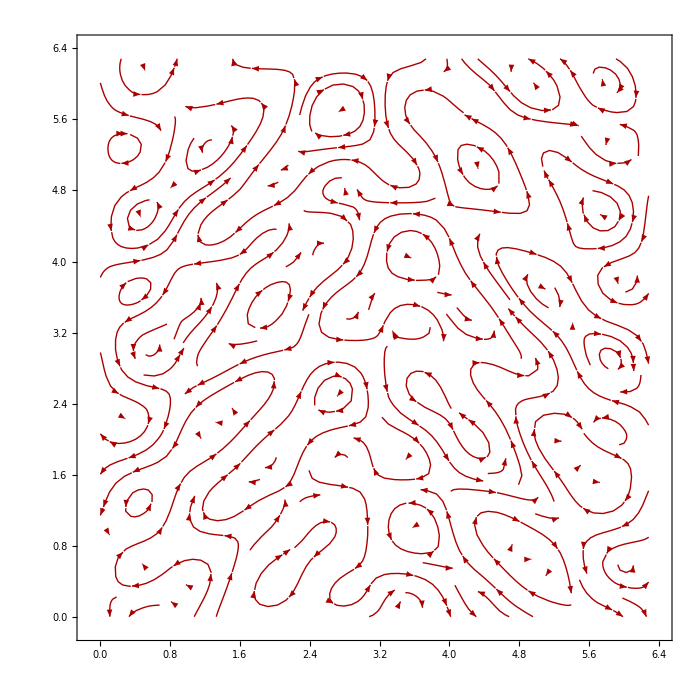

```mathematica
gs=StreamPlot[{u,v},{x,0,2π},{y,0,2π},StreamPoints->3000,PlotRangePadding->None,StreamStyle->Darker[Red],ImageSize->700,VectorStyle->Arrowheads[0]]
```

```mathematica
Manipulate[Show[ReliefPlot[ds⟦i⟧ᵀ,PlotRange->MinMax[ds],DataRange->{{0,2π},{0,2π}}],gs,PlotRange->{{0,2π},{0,2π}},ImageSize->700],{i,1,Length@ds,1}]
```

```mathematica
Dimensions@ds
```

{300,300,300}